# WORKSHOP 7: Cusp potential

Authors: Angel Salazar, Quray Potosi
School Of Physical Sciences and Nanotechnology

The solution of the incoming wave wave solution  ϕ_inc(x) is:

```mathematica
κ[a_,En_]:=ⅈ a  En;
μ[a_,En_]:=ⅈ a √(En^2-1);
```

```mathematica
ϕinc[a_,En_,V0_,x_]= c1 (2 ⅈ a V0)^(-1/2) Exp[-x/(2 a)] WhittakerM[κ[a,En],μ[a,En],2 ⅈ a V0 Exp[x/a]];
```

Then, the reflected ϕ_ref(x) solution is:

```mathematica
ϕref[a_,En_,V0_,x_]= c2 (2 ⅈ a V0)^(-1/2) Exp[-x/(2 a)] WhittakerM[κ[a,En],-μ[a,En],2 ⅈ a V0 Exp[x/a]];
```

Finally the transmitted solution ϕ_trans(x) can be written as

```mathematica
ϕtrans[a_,En_,V0_,x_]= c3(2 ⅈ a V0)^(-1/2) Exp[x/(2 a)] WhittakerM[κ[a,En],-μ[a,En],2 ⅈ a V0 Exp[-x/a]];
```

### Matching Conditions

```mathematica
eq1=ϕinc[a,En,V0,0]==ϕref[a,En,V0,0]+ϕtrans[a,En,V0,0];
```

```mathematica
eq2=(D[ϕinc[a,En,V0,x],x]/.x->0) ==(D[ϕref[a,En,V0,x],x]/.x->0)+(D[ϕtrans[a,En,V0,x],x]/.x->0 ) ;
```

```mathematica
sol=Solve[{eq1,eq2},{c2,c3}][[1]];
```

thus c2 is:

```mathematica
c2value [a_,En_,V0_]:=(c2/.sol)
```

and c3 is :

```mathematica
c3value[a_,En_,V0_]=(c3/.sol)
```

-((c1 (ⅈ WhittakerM[ⅈ a En,ⅈ a √(-1+En^2),2 ⅈ a V0] WhittakerM[1+ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0]-2 a En WhittakerM[ⅈ a En,ⅈ a √(-1+En^2),2 ⅈ a V0] WhittakerM[1+ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0]+2 a √(-1+En^2) WhittakerM[ⅈ a En,ⅈ a √(-1+En^2),2 ⅈ a V0] WhittakerM[1+ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0]-ⅈ WhittakerM[ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0] WhittakerM[1+ⅈ a En,ⅈ a √(-1+En^2),2 ⅈ a V0]+2 a En WhittakerM[ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0] WhittakerM[1+ⅈ a En,ⅈ a √(-1+En^2),2 ⅈ a V0]+2 a √(-1+En^2) WhittakerM[ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0] WhittakerM[1+ⅈ a En,ⅈ a √(-1+En^2),2 ⅈ a V0]))/(2 WhittakerM[ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0] (ⅈ WhittakerM[ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0]-2 a En WhittakerM[ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0]+2 a V0 WhittakerM[ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0]-ⅈ WhittakerM[1+ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0]+2 a En WhittakerM[1+ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0]-2 a √(-1+En^2) WhittakerM[1+ⅈ a En,-ⅈ a √(-1+En^2),2 ⅈ a V0])))

### Transmitted and Reflected coefficients.

The reflected coefficient is

```mathematica
Rfunc[a_,En_,V0_]:=Module[{c2v},c2v=c2value[a,En,V0];
Abs[c2v (2 I a V0)^(-μ[a,En])]^2/Abs[c1 (2 I a V0)^(μ[a,En])]^2];
```

The transmitted coefficient is

```mathematica
Tfunc[a_,En_,V0_]:=Module[{c3v},c3v=c3value[a,En,V0];
Abs[c3v (2 I a V0)^(-μ[a,En])]^2/Abs[c1 (2 I a V0)^(μ[a,En])]^2];
```

```mathematica
c1=1;
```

#### Test R+T=1

```mathematica
N[Rfunc[1,4,0.352]+Tfunc[1,4,0.352]/.{En->4.}]
```

0.999794

### Plot 1

```mathematica
V0=4;
a=1;
```

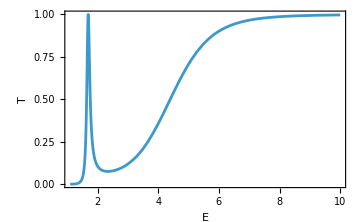

```mathematica
Plot[Evaluate@Tfunc[a,En,V0],{En,1.1,10},PlotRange->All,Frame->True,FrameLabel->{"E","T"},ImageSize->Medium]
```

### Plot 2

```mathematica
Clear[a,V0]
```

```mathematica
V0=4;
a= 2;
```

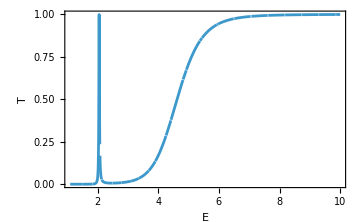

```mathematica
Plot[Evaluate@Tfunc[a,En,V0],{En,1.1,10},PlotRange->All,Frame->True,FrameLabel->{"E","T"},ImageSize->Medium]
```